```mathematica
?Range
```

Range[i_max] generates the list {1,2,…,i_max}. 
Range[i_min,i_max] generates the list {i_min,…,i_max}. 
Range[i_min,i_max,di] uses step di.

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[0, 10, 2]
```

{0,2,4,6,8,10}

```mathematica
x = Range[0, 2 Pi, 0.1]
```

{0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.,4.1,4.2,4.3,4.4,4.5,4.6,4.7,4.8,4.9,5.,5.1,5.2,5.3,5.4,5.5,5.6,5.7,5.8,5.9,6.,6.1,6.2}

```mathematica
Sin[Pi]
```

0

```mathematica
Sin[x]
```

{0.,0.0998334,0.198669,0.29552,0.389418,0.479426,0.564642,0.644218,0.717356,0.783327,0.841471,0.891207,0.932039,0.963558,0.98545,0.997495,0.999574,0.991665,0.973848,0.9463,0.909297,0.863209,0.808496,0.745705,0.675463,0.598472,0.515501,0.42738,0.334988,0.239249,0.14112,0.0415807,-0.0583741,-0.157746,-0.255541,-0.350783,-0.44252,-0.529836,-0.611858,-0.687766,-0.756802,-0.818277,-0.871576,-0.916166,-0.951602,-0.97753,-0.993691,-0.999923,-0.996165,-0.982453,-0.958924,-0.925815,-0.883455,-0.832267,-0.772764,-0.70554,-0.631267,-0.550686,-0.464602,-0.373877,-0.279415,-0.182163,-0.0830894}

```mathematica
y = Sin[x];
```

```mathematica
?ListPlot
```

ListPlot[{y_1,y_2,…}] plots points corresponding to a list of values, assumed to correspond to x coordinates 1, 2, …. 
ListPlot[{{x_1,y_1},{x_2,y_2},…}] plots a list of points with specified x and y coordinates. 
ListPlot[{list_1,list_2,…}] plots several lists of points.

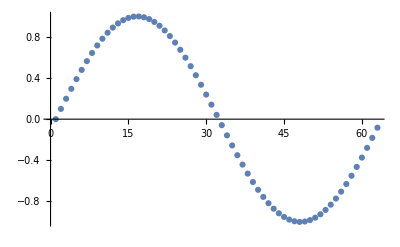

```mathematica
ListPlot[y]
```

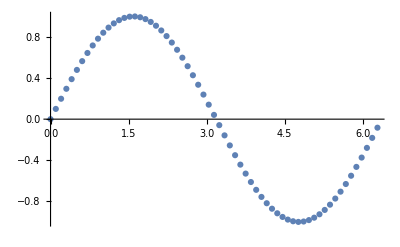

```mathematica
ListPlot[y, DataRange->{0, 2 Pi}]
```

```mathematica
Thread[{x, y}]
```

{{0.,0.},{0.1,0.0998334},{0.2,0.198669},{0.3,0.29552},{0.4,0.389418},{0.5,0.479426},{0.6,0.564642},{0.7,0.644218},{0.8,0.717356},{0.9,0.783327},{1.,0.841471},{1.1,0.891207},{1.2,0.932039},{1.3,0.963558},{1.4,0.98545},{1.5,0.997495},{1.6,0.999574},{1.7,0.991665},{1.8,0.973848},{1.9,0.9463},{2.,0.909297},{2.1,0.863209},{2.2,0.808496},{2.3,0.745705},{2.4,0.675463},{2.5,0.598472},{2.6,0.515501},{2.7,0.42738},{2.8,0.334988},{2.9,0.239249},{3.,0.14112},{3.1,0.0415807},{3.2,-0.0583741},{3.3,-0.157746},{3.4,-0.255541},{3.5,-0.350783},{3.6,-0.44252},{3.7,-0.529836},{3.8,-0.611858},{3.9,-0.687766},{4.,-0.756802},{4.1,-0.818277},{4.2,-0.871576},{4.3,-0.916166},{4.4,-0.951602},{4.5,-0.97753},{4.6,-0.993691},{4.7,-0.999923},{4.8,-0.996165},{4.9,-0.982453},{5.,-0.958924},{5.1,-0.925815},{5.2,-0.883455},{5.3,-0.832267},{5.4,-0.772764},{5.5,-0.70554},{5.6,-0.631267},{5.7,-0.550686},{5.8,-0.464602},{5.9,-0.373877},{6.,-0.279415},{6.1,-0.182163},{6.2,-0.0830894}}

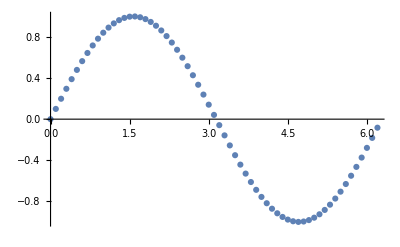

```mathematica
ListPlot[Thread[{x, y}]]
```

```mathematica
?Thread
```

RowBox[{"Thread", "[", RowBox[{StyleBox["f", "TI"], "[", StyleBox["args", "TI"], "]"}], "]"}] "threads" StyleBox["f", "TI"] over any lists that appear in StyleBox["args", "TI"]. 
RowBox[{"Thread", "[", RowBox[{RowBox[{StyleBox["f", "TI"], "[", StyleBox["args", "TI"], "]"}], ",", StyleBox["h", "TI"]}], "]"}] threads StyleBox["f", "TI"] over any objects with head StyleBox["h", "TI"] that appear in StyleBox["args", "TI"]. 
RowBox[{"Thread", "[", RowBox[{RowBox[{StyleBox["f", "TI"], "[", StyleBox["args", "TI"], "]"}], ",", StyleBox["h", "TI"], ",", StyleBox["n", "TI"]}], "]"}] threads StyleBox["f", "TI"] over objects with head StyleBox["h", "TI"] that appear in the first StyleBox["n", "TI"] StyleBox["args", "TI"].

```mathematica
?Table
```

Table[expr,n] generates a list of n copies of expr. 
Table[expr,{i,i_max}] generates a list of the values of expr when i runs from 1 to i_max. 
Table[expr,{i,i_min,i_max}] starts with i=i_min. 
Table[expr,{i,i_min,i_max,di}] uses steps di. 
Table[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Table[expr,{i,i_min,i_max},{j,j_min,j_max},…] gives a nested list. The list associated with i is outermost.

```mathematica
Table[{i, j}, {i, 5}, {j, 5}]
```

{{{1,1},{1,2},{1,3},{1,4},{1,5}},{{2,1},{2,2},{2,3},{2,4},{2,5}},{{3,1},{3,2},{3,3},{3,4},{3,5}},{{4,1},{4,2},{4,3},{4,4},{4,5}},{{5,1},{5,2},{5,3},{5,4},{5,5}}}

```mathematica
ListPlot[Table[{i, Sin[i]}, {i, 0, 2 Pi, 0.1}]]
```

-Graphics-

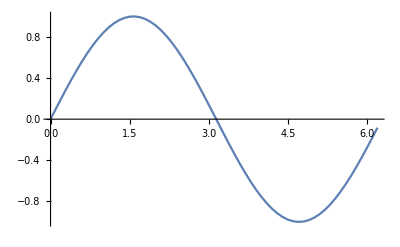

```mathematica
ListPlot[Table[{i, Sin[i]}, {i, 0, 2 Pi, 0.1}], Joined -> True]
```

```mathematica
ListLinePlot[Table[{i, Sin[i]}, {i, 0, 2 Pi, 0.1}]]
```

-Graphics-

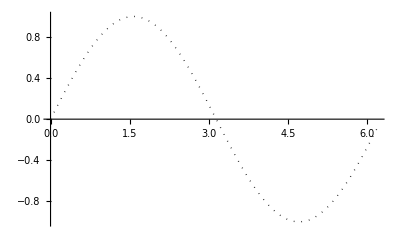

```mathematica
ListLinePlot[Table[{i, Sin[i]}, {i, 0, 2 Pi, 0.1}], PlotStyle->{Thick, Dotted, Black}]
```

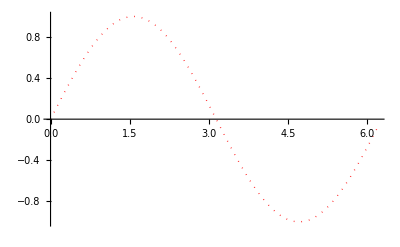

```mathematica
ListLinePlot[Table[{i, Sin[i]}, {i, 0, 2 Pi, 0.1}], PlotStyle->{Thick, Dotted, Red}]
```

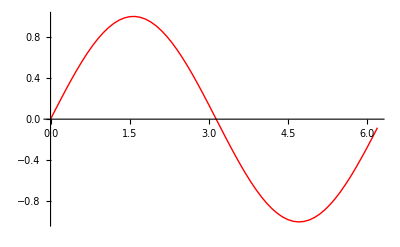

```mathematica
ListLinePlot[Table[{i, Sin[i]}, {i, 0, 2 Pi, 0.1}], PlotStyle->{Thick, Red}]
```

```mathematica
?Random
```

Random[] gives a uniformly distributed pseudorandom Real in the range 0 to 1. 
Random[type,range] gives a pseudorandom number of the specified type, lying in the specified range. Possible types are: Integer, Real and Complex. The default range is 0 to 1. You can give the range {min,max} explicitly; a range specification of max is equivalent to {0,max}.

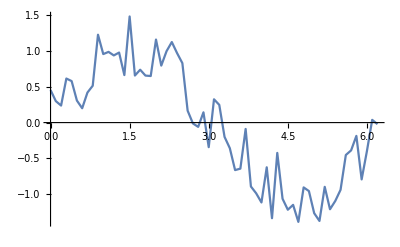

```mathematica
ListPlot[Table[{i, Sin[i] + Random[] - 0.5}, {i, 0, 2 Pi, 0.1}], Joined->True]
```

```mathematica
?Show
```

Show[graphics,options] shows graphics with the specified options added. 
Show[g_1,g_2,…] shows several graphics combined.

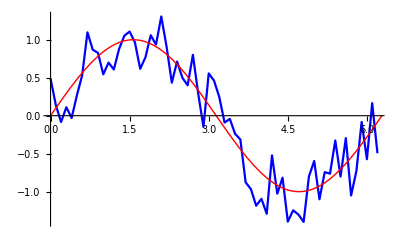

```mathematica
Show[ListPlot[Table[{i, Sin[i] + Random[] - 0.5}, {i, 0, 2 Pi, 0.1}], Joined->True, PlotStyle -> {Blue}]
         ,Plot[Sin[x], {x, 0, 2 Pi}, PlotStyle -> {Red, Thick}]]
```